This script allows you to simulate the predator-model that was introduced in the lecture for different values of the parameter K (prey carrying capacity). The output shows a phase-diagram including vector field, null-isoclines and one or two simulations; one starting from low initial densities (dark blue); the other starting from initial conditions close to the equilibrium point (if prey and predator can coexist). Next to the phase diagram, a timeseries plot show the dynamics of the prey density through time for each of these simulations.

```mathematica
drawPhasePlot[K_,T_:500.0]:=Module[{a, c, d, h, r, rhsP,rhsR,  eqlP, eqlR, maxP,maxR,pl1,pl2,pl3, sys, sol1,sol2,pl4a,pl4b,pl5a,pl5b},
(* set parameter values for fixed parameters *)
a = 0.5;
c = 1.0;
d = 0.1;
h = 0.2;
r = 1.0;
(* specify model equations *)
rhsP =r P(1-P/K)-a R P/(h+P);
rhsR = a c R P/(h+P)-d R;
(* draw null-isoclines *)
eqlP = (d h)/(a c-d);
eqlR = (a c K-d(h+K))/((a c-d)^2 K)r c h;
maxP=1.1Max[K,eqlP ];
maxR = 1.5((h+K)^2 r)/(4 a K);
pl1=ContourPlot[rhsP==0,{P,0,maxP},{R,0,maxR},PlotPoints->100,ContourStyle->{Dashed,Orange}];
pl2=ContourPlot[rhsR==0,{P,0,maxP},{R,0,maxR},PlotPoints->100,ContourStyle->{Dashed,Darker[Red]}];
(* plot vectorfield *)
pl3= StreamPlot[{rhsP,rhsR},{P,0,maxP},{R,0,maxR}, StreamStyle->LightGray];
(* plot trajectory *)
sys = Thread[{D[P[t],t],D[R[t],t]}==({rhsP,rhsR}/.{P->P[t],R->R[t]})];
sol1=NDSolve[Join[sys,{P[0]==0.001, R[0]==0.001}],{P[t],R[t]},{t,0,T}];
pl4a=ParametricPlot[{P[t],R[t]}/.sol1,{t,0,T},PlotStyle->Darker[Blue]];
pl4b=Plot[P[t]/.sol1,{t,0,T},PlotStyle->Darker[Blue],PlotRange->All];
If[eqlR > 0,
sol2=NDSolve[Join[sys,{P[0]==eqlP, R[0]==eqlR + 0.01}],{P[t],R[t]},{t,0,T}];
pl5a=ParametricPlot[{P[t],R[t]}/.sol2,{t,0,T},PlotStyle->Lighter[Blue]];
pl5b=Plot[P[t]/.sol2,{t,0,T},PlotStyle->Lighter[Blue],PlotRange->All];
GraphicsRow[{Show[pl3,pl1,pl2,pl4a,pl5a],Show[pl4b,pl5b]}],
GraphicsRow[{Show[pl3,pl1,pl2,pl4a],pl4b}]]
]
```

Here is an example of the output before the first bifurcation (appearance of an equilibrium where prey and predator can coexist)

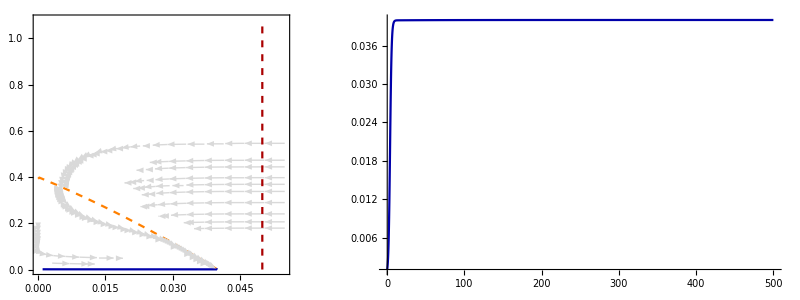

```mathematica
drawPhasePlot[0.04]
```

Here is an example of the output after the first bifurcation (appearance of an equilibrium where prey and predator can coexist), but before the second bifurcation (appearance of a stable limit cycle)

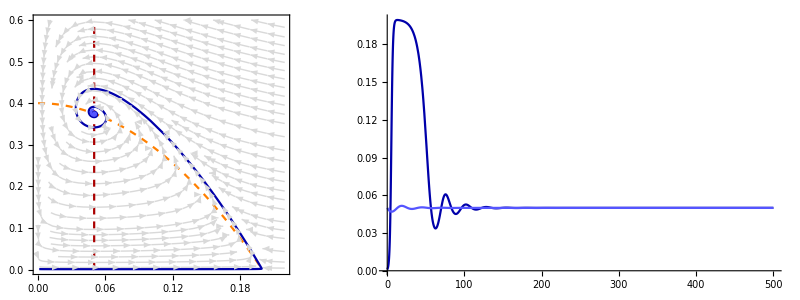

```mathematica
drawPhasePlot[0.2]
```

Here is an example of the output after the the second bifurcation (appearance of a stable limit cycle)

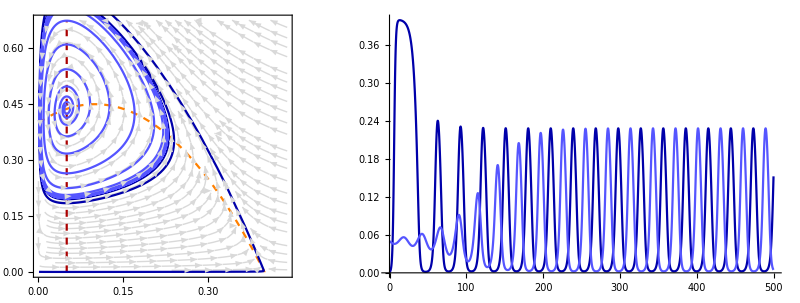

```mathematica
drawPhasePlot[0.4]
```

Use the manipulate function to slide continuously through the bifurcation sequence by varying the parameter K

```mathematica
Manipulate[drawPhasePlot[K],{{K,0.02},0.001,0.5}]
```